```mathematica
(*1 General N Problem (axial crystal, pseudopotential) - Monroe Data*)
```

```mathematica
Remove["Global`*"]
```

```mathematica
(*1.1 Get eigen*)		
		(*1.1.1 Set up variables*)
m=m0*{a,a,a,a,1};wmhz=2*Pi*1*^6;Num =Length[m];
kM =Append[ Array[k,{2,2}],{kz,kz}];kM=Transpose[Table[If[m[[i]]===m0,kM[[1;;,1]],kM[[1;;,2]]],{i,Num}]];
xM = Array[x,{3,Num}];
		(*1.1.2 Calculate Equilibrium Positions (axial crystal)*)
z0M = Array[z0,Num];
L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,Num}])
L0EQlist =L0EQ/@Range[Num]//FullSimplify;
guessz0=Range[-3.5,3.5,7/(Num-1)];pos=Transpose[Append[{z0M},guessz0]];z0M=z0M/.Chop[FindRoot[L0EQlist,pos]];
L0Mn[i_,j_,n_]:=If[i==j,0,Abs[z0M[[i]]-z0M[[j]]]^n]
		(*1.1.3 Create matrix*)
ke2=2.306569*^-28;l0=(ke2/kz)^(1/3);
ics=ArrayReshape[Append[Table[xM[[d,i]]->0,{d,2},{i,Num}],Table[(xM[[3,i]]-xM[[3,j]])->L0Mn[i,j,1]*l0,{i,Num},{j,i+1,Num}]],{2*Num+Num*(Num-1)/2}];
Uel=Total[0.5*kM*(xM^2),2]+ke2*Sum[(Total[(xM[[;;,i]]-xM[[;;,j]])^2])^(-0.5),{i,Num},{j,i+1,Num}];
Vel1=-Table[D[Uel,{xM[[d,i]]},{xM[[d,j]]}]/Sqrt[m[[i]]*m[[j]]],{d,3},{i,Num},{j,Num}]/.ics//FullSimplify;
Vel1norm=Vel1/.{a->1,k[1,2]->k[1,1],k[2,2]->k[2,1]};
		(*1.1.4 Subbing in mass & secular frequency values*)
k[1,1]=3.25*^-40/m0*V0^2/w^2/r0^4+1.602*^-13*(V1/r0^2-κ*U/z0^2)//FullSimplify;
k[1,2]=3.25*^-40/a/m0*V0^2/w^2/r0^4+1.602*^-13*(V1/r0^2-κ*U/z0^2)//FullSimplify;
k[2,1]=3.25*^-40/m0*V0^2/w^2/r0^4+1.602*^-13*(-V1/r0^2-κ*U/z0^2)//FullSimplify;
k[2,2]=3.25*^-40/a/m0*V0^2/w^2/r0^4+1.602*^-13*(-V1/r0^2-κ*U/z0^2)//FullSimplify;
kz=3.204*^-13*κ*U/z0^2//FullSimplify;
```

```mathematica
(*1.1.5 sub in values and find eigen*)
Clear[V0,U,w];
ahold=1.23913;m0=138*1.66054*^-27;κ=1;V1=0;r0=0.2;z0=0.4;
eigenholder=Table[Eigensystem[Vel1[[d]]/.{a->ahold}],{d,3}];
wmlist=Sqrt[-eigenholder[[;;,1]]]/wmhz//FullSimplify;vlist=eigenholder[[;;,2]]//FullSimplify;

eigenholder=Table[Eigensystem[Vel1[[d]]/.{a->1}],{d,3}];
wmlistnorm=Sqrt[-eigenholder[[;;,1]]]/wmhz//FullSimplify;vlistnorm=Chop[eigenholder[[;;,2]]/.{V0->1,V1->0,U->1,w->1}//FullSimplify];
a=ahold;
```

```mathematica
(*1.1.8 Generate Monroe solutions*)
uholder=NSolve[Sqrt[kz/a/m0]==0.16*wmhz,U];vholder=NSolve[Sqrt[k[1,2]/a/m0]==3.06*wmhz/.uholder/.w->28.3,V0];
solnsMONROE={vholder[[1,1]],uholder[[1,1]],w->28.3}

wmlist[[1]]/.solnsMONROE/.{w->28.3}
wmlist[[3]]/.solnsMONROE/.{w->28.3}
```

{V0→343.043,U→0.143309,w→28.3}

{3.78577,3.05884,3.05216,3.04352,3.03399}

{0.588213,0.494982,0.399427,0.288458,0.163006}

```mathematica
(*1.2 Optimizing parameters*)
```

```mathematica
(*1.2.1 Optimization prep*)
qmax=0.4;tempK=0.1;safetyfactor=0.99;constrmax = 1*^40;
zigzag=AllTrue[wmlist[[1]],Im[#]==0&]//FullSimplify;resids=Total[(vlist[[1,;;,1;;Num-1]]-vlistnorm[[1,;;,1;;Num-1]])^2,2];

trapConstr={100≤V0≤2000,0<U<(2.02918*^-27*(V0/w/r0)^2/a/m0-V1)*(z0/r0)^2/3*safetyfactor,10≤w≤40};
kConstr={k[1,2]>kz,k[2,2]>kz,8.11582681*^-27/m0/qmax*V0<(r0*w)^2}//FullSimplify;
```

```mathematica
(*1.2.2 Optimize for least squares*)
vlsqx[V0s_, Us_,ws_]:=If[zigzag/.{V0->V0s,U->Us,w->ws},resids/.{V0->V0s,U->Us,w->ws},constrmax];
solnsLSQ=NMinimize[{vlsqx[V0,U,w],kConstr[[3]],trapConstr},{V0,U,w},MaxIterations->10000][[2]];
{MatrixForm[solnsLSQ],MatrixForm[vlist[[1]]/.solnsLSQ],MatrixForm[wmlist[[1]]/.solnsLSQ],MatrixForm[{k[1,1],k[1,2]}/.solnsLSQ]}
{MatrixForm[kConstr/.solnsLSQ]}
```

NMinimize::nnum: The function value Indeterminate is not a number at {U,V0,w} = {9.74325×10^-8,100.,36.9665}.

{(V0→235.548
U→1.83686
w→40.),(0.0528159 | 0.0904343 | 0.158596 | 0.319545 | 1.
-3.22998 | -2.59246 | -1.88499 | -0.926342 | 1.
2.94237 | -0.748335 | -2.39296 | -2.21633 | 1.
-2.1074 | 4.24317 | 0.347517 | -4.15447 | 1.
1.55396 | -6.96357 | 10.7666 | -6.75919 | 1.),(1.65106
1.38411
1.17061
0.846836
0.0796415),(2.88988×10^-11
2.2967×10^-11)}

{(True
True
True)}

```mathematica
(*1.2.3 Fixed q-parameter*)
 (*Enter constraints here: qset sets q-parameter value*)
qset=0.4;qholder=8.11582681*^-27/m0/qset/r0^2;
fqtrapConstr={Max[{100,10^2/qholder}]≤V0≤Min[{2000,40^2/qholder}],0<U<(2.02918*^-27*(V0/w/r0)^2/a/m0-V1)*(z0/r0)^2/3*safetyfactor}/.{w->Sqrt[qholder*V0]}//FullSimplify;

vfqlsqx[V0s_, Us_]:=If[zigzag/.{V0->#1,U->#2,w->#3},resids/.{V0->#1,U->#2,w->#3},constrmax]&[V0s,Us,Sqrt[qholder*V0s]];

solnsfqLSQ=NMinimize[{vfqlsqx[V0,U],fqtrapConstr},{V0,U},MaxIterations->1000][[2]];
solnsfqLSQ=Append[%,w->Sqrt[qholder*V0]/.%];

{MatrixForm[solnsfqLSQ],MatrixForm[vlist[[1]]/.solnsfqLSQ],MatrixForm[wmlist[[1]]/.solnsfqLSQ],MatrixForm[{k[1,1],k[1,2]}/.solnsfqLSQ]}
{MatrixForm[kConstr/.solnsfqLSQ],MatrixForm[lConstr/.solnsfqLSQ]}
8.11582681*^-27/m0*V0/(r0*w)^2/.solnsfqLSQ
```

$Aborted

ReplaceAll::reps: {$Aborted} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Append::normal: Nonatomic expression expected at position 1 in Append[$Aborted,w→1.48779 √V0/.$Aborted].

ReplaceAll::reps: {Append[$Aborted,w→1.48779 √V0/.$Aborted]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{Append[$Aborted,w→1.48779 √V0/.$Aborted],1,1,{0.-1.00125×10^-12 U+(8.86411×10^-13 V0^2)/w^2,0.-1.00125×10^-12 U+(7.15349×10^-13 V0^2)/w^2}/.Append[$Aborted,w→1.48779 √V0/.$Aborted]}
 |  |  |  |

ReplaceAll::reps: {Append[$Aborted,w→1.48779 √V0/.$Aborted]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{1. V0^2 w^2>4.199 U w^4,1. V0^2 w^2>4.199 U w^4,1. V0<0.451768 w^2}/.Append[$Aborted,w→1.48779 √V0/.$Aborted],lConstr/.Append[$Aborted,w→1.48779 √V0/.$Aborted]}

ReplaceAll::reps: {Append[$Aborted,w→1.48779 √V0/.$Aborted]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(0.88541 V0)/w^2/.Append[$Aborted,w→1.48779 √V0/.$Aborted]

```mathematica
solnsMONROE={V0->343.04,U->0.14331,w->28.3};
```

```mathematica
(*Print solutions*)
solnsDJ=solnsMONROE; (*Enter which solution you want formatted: solnsLSQ for least squares, solnsQRMS for root mean square position*)
			(*trap/ion parameters*)
eigenholder2=Table[Eigensystem[Vel1[[d]]/.solnsDJ],{d,3}];wmvals=Sqrt[-eigenholder2[[;;,1]]]/wmhz//FullSimplify;
vvals=Table[Normalize[eigenholder2[[d,2,i]]],{d,3},{i,Num}]//FullSimplify;
wsecvals={{Sqrt[k[1,1]/m0],Sqrt[k[1,2]/m0/a]},{Sqrt[k[2,1]/m0],Sqrt[k[2,2]/m0/a]},{Sqrt[kz/m0],Sqrt[kz/m0/a]}}/wmhz/.solnsDJ;
qx=8.11582681*^-27*V0/w^2/r0^2/m0/{1,a}/.solnsDJ;
			(*rms position fluctuation*)
gim=Table[Transpose[vvals[[d]]],{d,3}];fwm=1/wmvals[[1]]/wmhz*(1/(Exp[wmvals[[1]]*4.8*^-5/tempK]-1)+0.5);
rmsq2=Sqrt[(gim[[1]]^2).fwm*5.2728*^-35/m];
			(*format 1*)
res1=Table[{MatrixForm[vvals[[d,j]]],wmvals[[d,j]]},{d,3},{j,Num}];
wmlistnorm=
normres1=Chop[Table[{MatrixForm[Normalize[vlistnorm[[1,i]]]],wmlistnorm[[1,i]]}/.solnsDJ,{i,Num}]];
res2=Transpose[{wsecvals[[1,;;2]],wsecvals[[2,;;2]],wsecvals[[3,;;2]],qx[[;;2]]}];
			(*format 2*)
MatrixForm[solnsDJ]
TableForm[{{TableForm[res1[[1]],TableHeadings->{None,{"Eigenvector", "Mode Freq.(x2π MHz)"}}],TableForm[normres1,TableHeadings->{None,{"Eigenvector", "Mode Freq.(x2π MHz)"}}]}},TableHeadings->{None,{"Mixed-Species","Single-Species"}}]
TableForm[res2,TableHeadings->{{"Atom","Molecule"},{"x-ω_sec(x2π MHz)", "y-ω_sec(x2π MHz)","z-ω_sec(x2π MHz)", "q_x-parameter"}}]
TableForm[Transpose[{rmsq2}],TableHeadings->{Table[TextString[m[[i]]/m0],{i,Num}],{"√(<q^2>)@0.1K"}}]
```

General::ivar: 0 is not a valid variable.

(V0→343.043
U→0.143309
w→28.3)

Mixed-Species | Single-Species
Eigenvector | Mode Freq.(x2π MHz)
(0.000139933
0.00035352
0.00113059
0.00723176
0.999973) | 3.78577
(-0.631341
-0.547561
-0.450906
-0.313465
0.00305869) | 3.05884
(0.679189
-0.0741916
-0.475781
-0.553904
0.00447493) | 3.05216
(0.35765
-0.6745
-0.122543
0.634115
-0.00425893) | 3.04352
(0.110439
-0.489615
0.745183
-0.439063
0.0024904) | 3.03399 | Eigenvector | Mode Freq.(x2π MHz)
(0.447984
0.450548
0.453752
0.458767
0.424216) | 3.78577
(-0.664656
-0.289624
0.0366208
0.349554
0.592302) | 3.05884
(0.517178
-0.330378
-0.513441
-0.196689
0.56663) | 3.05216
(-0.282132
0.624128
-0.0436025
-0.630137
0.363168) | 3.04352
(0.102332
-0.463076
0.726116
-0.481233
0.127509) | 3.03399

| x-ω_sec(x2π MHz) | y-ω_sec(x2π MHz) | z-ω_sec(x2π MHz) | q_x-parameter
Atom | 3.79224 | 3.79224 | 0.178106 | 0.379245
Molecule | 3.06 | 3.06 | 0.16 | 0.306057

| √(<q^2>)@0.1K
1.23913 | 8.12629×10^-8
1.23913 | 8.14669×10^-8
1.23913 | 8.15363×10^-8
1.23913 | 8.14668×10^-8
1.0 | 7.29621×10^-8

```mathematica
(*Bar graphs a la Monroe*)
monxplot=Table[BarChart[vvals[[1,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
monzplot=Table[BarChart[vvals[[3,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[3,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
```

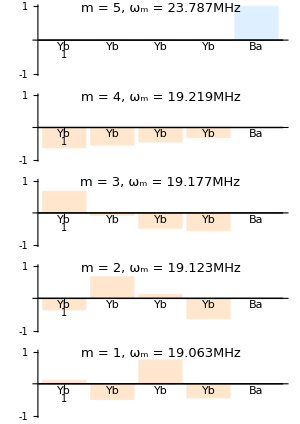
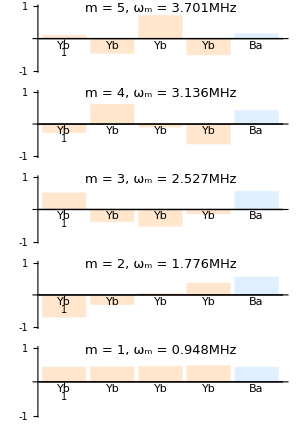

```mathematica
{GraphicsColumn[monxplot,Frame->All,ImageSize->300],GraphicsColumn[monzplot,Frame->All,ImageSize->300]}
```

```mathematica
lsqxplot=Table[BarChart[vvals[[1,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
lsqzplot=Table[BarChart[vvals[[3,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wmvals[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
```

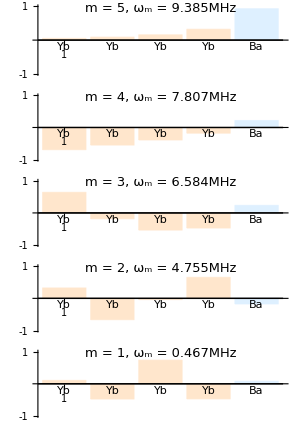
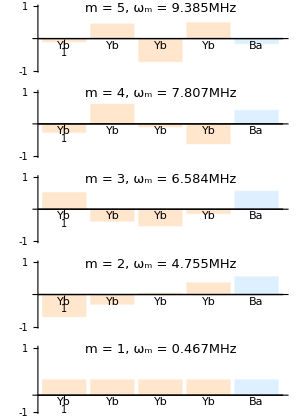

```mathematica
{GraphicsColumn[lsqxplot,Frame->All,ImageSize->300],GraphicsColumn[lsqzplot,Frame->All,ImageSize->300]}
```

```mathematica
vthde=Chop[Table[Normalize[vlistnorm[[d,i]]]/.solnsLSQ,{d,3},{i,Num}]];
wthde=wmlistnorm/.solnsLSQ;
nx=Table[BarChart[vthde[[1,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightOrange},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wthde[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num}];
nz=Table[BarChart[vthde[[3,i]],PlotRange->{-1,1},Ticks->{{-1,0,1}},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightOrange},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/4,Epilog->Text[Style["m = "<>ToString[Num-i+1]<>", ω_m = "<>ToString[NumberForm[2*Pi*wthde[[1,i]],{∞,3}]]<>"MHz", Black, 13],Scaled[{.5,.9}]]],{i,Num}];
```

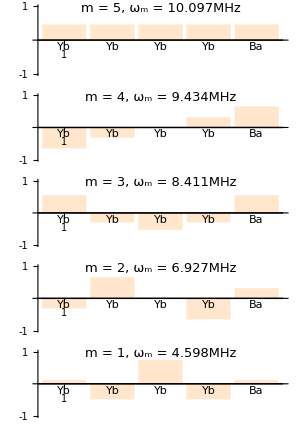
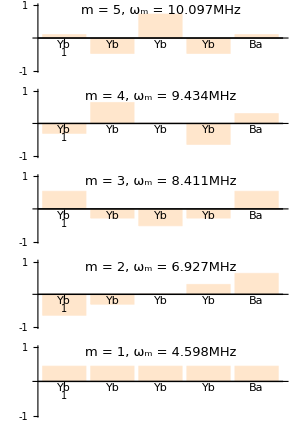

```mathematica
{GraphicsColumn[nx,Frame->All,ImageSize->300],GraphicsColumn[nz,Frame->All,ImageSize->300]}
```